2 May 2020

# Computational Thinking

## An Exploration of Books in the Wolfram Language

## Martins Samuel PhD Candidate, Queen’s University Belfast

## Introduction

Computational thinking

Problem decomposition: breaking down a problem into sub-problems

Pattern recognition: noticing similarities, differences, properties, or trends in data

Pattern generalization: extracting out unnecessary details and generalize those that are necessary in order to define a concept or idea in general terms

Algorithm design: building a repeatable procedure to solve a particular problem

Wolfram Language

Thousands of powerful in built functions

```mathematica
WolframLanguageData[]//Length
```

5605

But if you need it, there’s Python, Java Script, Julia, R and Ruby!

import numpy as np
a = np.arange(15).reshape(3, 5)
print(a)

[[ 0  1  2  3  4]

[ 5  6  7  8  9]

[10 11 12 13 14]]

Vast amount of live, real-world computable data and entities

```mathematica
WeatherData["Lagos","Temperature"]
```

29 °C

```mathematica
With[{data=EntityValue[Entity["Satellite","25544"],{"Position","PositionLine"}]},
GeoGraphics[{Gray,Thickness[.005],Arrowheads[{{0.05,0.4},{0.05,0.13}}],Arrow@@data⟦2⟧,Red,PointSize[.01],Point[data⟦1⟧],Opacity[.1],Black,GeoVisibleRegion[data⟦1⟧]},GeoCenter->data⟦1⟧,GeoRange->"World"]]
```

-Graphics-

Automation and interactive computation

```mathematica
WolframAlpha["sun path, Lagos"]
```

WolframAlphaQueryResults

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
DynamicGeoGraphics[GeoMarker@Entity["City",{"CapeTown","WesternCape","SouthAfrica"}],ImageSize->300]
```

```mathematica
Video["ExampleData/Caminandes.mp4",Appearance->"Basic",ImageSize->300]
```

Video[ExampleData/Caminandes.mp4,Appearance→Basic,AudioOutputDevice→Automatic,ImageSize→300,SoundVolume→Automatic]ExampleData/Caminandes.mp4Basic1StandardForm

Data analysis and machine learning

```mathematica
SpeechRecognize[]
```

right then perfect timing

```mathematica
ImageCases[-Graphics-]
```

<|domestic cat→{-Graphics-},domestic dog→{-Graphics-}|>

Desktop, Cloud, Raspberry Pi, etc.

Exploration topic: books

```mathematica
Interpreter["Book"|"ComputedBook"]["Ake: The Years of Childhood"]
```

Aké: The Years of Childhood

```mathematica
EntityValue[%["Author"],"Dataset"]
```

## Book entities

In the Wolfram Language real-word data are represented in the form of Entities.

```mathematica
(* we have 12,361 entities (as of 02.05.2020) *)
allWLBooks=EntityList["Book"];
```

```mathematica
{Highlighted@Length@allWLBooks,RandomSample[allWLBooks,20]}
```

{12361,{"...and Ladies of the Club",The Ground Truth: The Untold Story of America Under Attack on 9/11,The Bachelor Machine,The Old Devils,The Mystery of the Missing Mascot,Captain Jack,The Discovery of the Unconscious: The History and Evolution of Dynamic Psychiatry,The Robots of Dawn,According to Jake and the Kid,The Flying Saucer Mystery,King of the Rainy Country,Notes on a Scandal,Amorality Tale,This Republic of Suffering: Death and the American Civil War,The Salmon of Doubt,The Golden Bowl,Ashanti to Zulu: African Traditions,The Masters and the Slaves: A Study in the Development of Brazilian Civilization,Here Today,Clear and Present Dangers: A Conservative View of America's Government}}

### Entity properties

The properties of Entities can be gotten using Entity Properties.

```mathematica
(* book entity properties *)
bookProps=EntityProperties["Book"]
Length@%
```

{author,awards,English plain text,entity classes,first publication date,image,title,original language,original title,plain text,publisher}

11

```mathematica
(* see the properties of a random book *)
book=RandomChoice@allWLBooks
EntityValue[book,"Dataset"]
```

Indian Fighter

```mathematica
(* we can also get author entity properties *)
author=If[Length[#]==1,#⟦1⟧,#]&@book[EntityProperty["Book","Author"]]
```

F.F. Halloran

```mathematica
(* This entity type is Person *)
EntityTypeName[author]
```

Person

```mathematica
(* and all persons belong to the entity class People (there are about half a million entities in this class) *)
EntityClassList["Person"]
```

{people}

```mathematica
authorProps=EntityProperties["Person"]
Highlighted@Length@%
```

{other names,astrological sign,date of birth,place of birth,brothers,children,Chinese zodiac sign,daughters,date of death,place of death,entity classes,father,full name,gender,height,husbands,image,space missions,mathematical contributions,mother,notable film appearances,notable film direction credits,notable film production credits,notable film writing credits,name,nationality,net worth,notable artworks,astronomical discoveries,notable books,famous chemistry problems,notable facts,notable inventions,physics contributions,occupation,parents,siblings,sisters,sons,spouses,weight,wives}

42

```mathematica
(* we have 42 properties for each person. we can extend the data we have on each book with this data *)
EntityValue[author,"Dataset"]
```

Now, let’s create a function which conjoins the data on a given book and the data on its author into one dataset

```mathematica
bookAuthorAssoc=Block[{bookAssoc,bookAuthor,authorAssoc},
bookAssoc=EntityValue[book,"Association"];
bookAuthor=bookAssoc[EntityProperty["Book","Author"]];
authorAssoc=EntityValue[bookAuthor,"Association"];
<|"Book"->bookAssoc,"Author"->authorAssoc|>
];
```

```mathematica
(* so we have one dataset for book and author(s) *)
Dataset@bookAuthorAssoc
```

### Entity filtering

What if a book has more than one author, what will the dataset for that look like?

```mathematica
(* a function which gets us all books with ≥10 authors *)
tenOrMoreAuthorsEntityClass=FilteredEntityClass["Book",EntityFunction[aLen, Length[aLen[EntityProperty["Book","Author"]]]≥10]]
```

FilteredEntityClass[Book,EntityFunction[aLen,Length[aLen[author]]≥10]]

```mathematica
(* books which match our criteria *)
EntityList[tenOrMoreAuthorsEntityClass]
```

{Atlanta Nights,Earth (The Book): A Visitor's Guide to the Human Race,Halo: Evolutions - Essential Tales of the Halo Universe}

```mathematica
(* result:  *)
```

```mathematica
(* extended book-author(s) dataset *)
bookAuthorAssoc2=Block[{bookAssoc,bookAuthor,authorAssoc},
bookAssoc=EntityValue[Entity["Book","AtlantaNights"],"Association"];
bookAuthor=bookAssoc[EntityProperty["Book","Author"]];
authorAssoc=EntityValue[bookAuthor,"Association"];
<|"Book"->bookAssoc,"Author"->authorAssoc|>
];
```

```mathematica
Dataset@bookAuthorAssoc2
```

## Problem: how do we quickly and accurately arrange books on a bookshelf according to the colours of their covers

Image Source: Shawn & Lindsey’ s Best Friends Guide to Everything

If we have some data for the books on the bookshelf then we may be able to solve the problem using computational thinking.

## 1. Problem decomposition: “arrange” → “sort”

First, we need to break the problem down and think about how we can apply the data we have to solve it.

```mathematica
randInt=RandomInteger[100,100]
```

{88,76,63,10,42,21,0,37,20,61,62,39,79,94,64,40,58,6,53,59,98,49,28,52,84,78,22,73,8,11,47,54,65,61,51,51,56,90,90,70,27,4,20,38,67,36,14,20,3,30,87,60,6,62,77,54,100,65,24,89,8,1,81,24,30,25,7,13,2,13,8,93,91,79,90,74,47,50,28,35,37,44,95,94,59,26,40,90,54,30,100,29,83,59,91,8,78,7,81,94}

```mathematica
Sort@randInt
```

{0,1,2,3,4,6,6,7,7,8,8,8,8,10,11,13,13,14,20,20,20,21,22,24,24,25,26,27,28,28,29,30,30,30,35,36,37,37,38,39,40,40,42,44,47,47,49,50,51,51,52,53,54,54,54,56,58,59,59,59,60,61,61,62,62,63,64,65,65,67,70,73,74,76,77,78,78,79,79,81,81,83,84,87,88,89,90,90,90,90,91,91,93,94,94,94,95,98,100,100}

```mathematica
(* sorting in this case is based on R, G, B values *)
Manipulate[Graphics[{RGBColor[r,g,b],Rectangle[]}],
{r,0,1},
{g,0,1},
{b,0,1},ControlType->Slider,ControlPlacement->Left]
```

```mathematica
randCol=RandomColor[(*RGBColor[1,_,_],*)100]
```

{RGBColor[0.06254774394923213, 0.7055199466641167, 0.597425099563583],RGBColor[0.3998279778581588, 0.04091153171013384, 0.9121431811506671],RGBColor[0.3425668475777961, 0.9107370039860723, 0.6393607549449398],RGBColor[0.7713551286802083, 0.28399558246413936, 0.5502104581803633],RGBColor[0.2001662337492549, 0.38059352917792943, 0.23080469276695736],RGBColor[0.7447282022134654, 0.24819962039461796, 0.21067618126441578],RGBColor[0.05855646548365123, 0.2779330085993166, 0.4592186043783537],RGBColor[0.8625230663370447, 0.8757557224247512, 0.260217925561792],RGBColor[0.9262612937767396, 0.32818075068391317, 0.09104096966485642],RGBColor[0.7559593802047064, 0.46268727715762514, 0.28774777438237376],RGBColor[0.29423701942797287, 0.5169749037351026, 0.7740008949429547],RGBColor[0.6700450440804497, 0.5867657124933279, 0.7322668150893357],RGBColor[0.3782868272978437, 0.9099646604167508, 0.3631507446754558],RGBColor[0.4640166600657343, 0.950150296476487, 0.25119293660310094],RGBColor[0.9313757105778484, 0.8393895056708938, 0.0859477259229462],RGBColor[0.03294301856214843, 0.8108094787681737, 0.746874748434563],RGBColor[0.6123525477231233, 0.602485880195841, 0.3238656448656474],RGBColor[0.8928780166549917, 0.2944470848790808, 0.660635086307402],RGBColor[0.10301756442402876, 0.2092290551569549, 0.8855198331648177],RGBColor[0.30760291147017615, 0.47066002415807895, 0.2319463899147296],RGBColor[0.7577340500655501, 0.40341604935423714, 0.24301284800916467],RGBColor[0.3935423970672922, 0.7205939269545083, 0.9606875424176724],RGBColor[0.13186422111133966, 0.7516394857182533, 0.817128810109335],RGBColor[0.22146671508127258, 0.153023844113225, 0.7677473819132961],RGBColor[0.9942617168090497, 0.5622839727332147, 0.18709862421981382],RGBColor[0.0891191259135895, 0.09976282976976925, 0.4718088041935251],RGBColor[0.9883818560487956, 0.13576076760349176, 0.45922970330877755],RGBColor[0.000043972881083265136, 0.8446962244421978, 0.8768478803732254],RGBColor[0.971641955090947, 0.37098783452889283, 0.6223460767925639],RGBColor[0.6138039488427487, 0.8435132289406126, 0.7872742089656701],RGBColor[0.23637432092040478, 0.513007663269772, 0.20952927935180288],RGBColor[0.18025529303823928, 0.2919478949867558, 0.24836093596548103],RGBColor[0.8095999020272957, 0.8918254326984123, 0.6225612136300618],RGBColor[0.9913755801544373, 0.9426174060519363, 0.43698429516722426],RGBColor[0.523305857576946, 0.6973329735964862, 0.3268566019345238],RGBColor[0.10705845437328909, 0.3979884211353746, 0.6906292780966983],RGBColor[0.3854086510054091, 0.3683619468981736, 0.28317003065685453],RGBColor[0.16398198512195772, 0.2937002626523848, 0.21003317356411721],RGBColor[0.4233714112867626, 0.17173362757223853, 0.09718224997322267],RGBColor[0.16773331956332282, 0.168223903275325, 0.518300922079854],RGBColor[0.9950796601140932, 0.3000715451631666, 0.6235978293933553],RGBColor[0.10243329996337547, 0.8199311636037783, 0.10135669051080631],RGBColor[0.21237743479844529, 0.025537075379648888, 0.9332292804705717],RGBColor[0.8234131621697209, 0.3462535544319263, 0.6941335544967886],RGBColor[0.4685155854581595, 0.6129591714968949, 0.3228650193985201],RGBColor[0.011268028804378716, 0.5761495211526422, 0.4170414532421647],RGBColor[0.9659449087344945, 0.9988746428308939, 0.4256836830797024],RGBColor[0.6949702511992493, 0.5583910467342579, 0.2874004896388176],RGBColor[0.7580898008030776, 0.36446183380274744, 0.1676282465849115],RGBColor[0.7216053425703803, 0.1069467420949759, 0.4166090354628733],RGBColor[0.04767734442461635, 0.8659261859183867, 0.2223743231418165],RGBColor[0.2224089911647289, 0.3183798424464741, 0.5761309399025378],RGBColor[0.3108452227207741, 0.9600074748706173, 0.4224786247892598],RGBColor[0.9589184316613024, 0.22045761214438242, 0.8782353547924411],RGBColor[0.06589623212868356, 0.6836579065877348, 0.2662657793775782],RGBColor[0.0773153642038058, 0.7524875517462939, 0.21770399374626126],RGBColor[0.9906092491840752, 0.9614813055280895, 0.7935975121177001],RGBColor[0.8646275620992383, 0.1330719521519863, 0.9342183175225665],RGBColor[0.6174941277678061, 0.3710147410675477, 0.6446337095493198],RGBColor[0.8185136261546617, 0.21487395324282366, 0.2566551621116644],RGBColor[0.259855913159345, 0.016991582657156723, 0.6488457849814231],RGBColor[0.5372452559549821, 0.9542829549565757, 0.4887150193872394],RGBColor[0.4001569876297264, 0.76934032363833, 0.37631199122504944],RGBColor[0.10309552603583372, 0.524430232278774, 0.9744751265437503],RGBColor[0.4091134412782851, 0.42340212364383234, 0.9206689717382956],RGBColor[0.2880402063296621, 0.2651865299921534, 0.38237410525219406],RGBColor[0.38649022083727136, 0.7789835940633869, 0.9086818202130009],RGBColor[0.4879523207767704, 0.48665265345439135, 0.37102198052626667],RGBColor[0.1123154400847659, 0.45316873234192845, 0.8205041468527623],RGBColor[0.6817699656346239, 0.7734325342558201, 0.8400975229665166],RGBColor[0.11487569771324058, 0.006404786879230073, 0.3208212624659914],RGBColor[0.03972738399583098, 0.3879042020295804, 0.6585214166641922],RGBColor[0.6641881295049352, 0.9165017581026016, 0.9642419108441189],RGBColor[0.8787817632997967, 0.9824615734409439, 0.9491242225250256],RGBColor[0.02418447194314277, 0.7720516823949881, 0.14185521493724873],RGBColor[0.218840607105802, 0.43747449566413743, 0.7273183310828195],RGBColor[0.42598312525461157, 0.1356788923102188, 0.1336209337360632],RGBColor[0.6802142693560824, 0.6255162145157633, 0.8769053484969711],RGBColor[0.9661037669470702, 0.23455800338544375, 0.7318363724357573],RGBColor[0.6510737573878738, 0.9825805829810557, 0.8979615846605531],RGBColor[0.004209236419780327, 0.6176510808055338, 0.42872911377189404],RGBColor[0.9894813216086964, 0.5081738283041066, 0.04254585635846175],RGBColor[0.5992316843895935, 0.2990916565527353, 0.08678928223639137],RGBColor[0.03988389199449771, 0.4350025949999794, 0.8112446869046761],RGBColor[0.5212309604193759, 0.5494477261374191, 0.7211549558010322],RGBColor[0.416144557561956, 0.6950125438945796, 0.330634101709649],RGBColor[0.44108851348564637, 0.1373582344629165, 0.709673999165245],RGBColor[0.6346595576691869, 0.8035099275224336, 0.6070243933527364],RGBColor[0.32668575860772076, 0.6569780821915745, 0.4147488099582959],RGBColor[0.5312252191876161, 0.13640914811330251, 0.045749128615603984],RGBColor[0.8380551031655838, 0.23660407077351464, 0.8135820245568637],RGBColor[0.7851719836046043, 0.4865192847180835, 0.7949396710921981],RGBColor[0.09881723081151517, 0.5604915044215761, 0.8100638200771422],RGBColor[0.06058402939089835, 0.9397110769127117, 0.6360744752602536],RGBColor[0.3120704626340527, 0.5570333607502129, 0.8034842017272883],RGBColor[0.12488800321176985, 0.580720232000872, 0.6660041687381697],RGBColor[0.5183984439638374, 0.916507361372203, 0.3670180109582881],RGBColor[0.7479500820366884, 0.9131052292021316, 0.5530852237137442],RGBColor[0.8047780542422325, 0.4027656490355205, 0.9451203026745787],RGBColor[0.39371418564877914, 0.45821719901328994, 0.11267942381678675]}

```mathematica
Sort@randCol
```

{RGBColor[0.000043972881083265136, 0.8446962244421978, 0.8768478803732254],RGBColor[0.004209236419780327, 0.6176510808055338, 0.42872911377189404],RGBColor[0.011268028804378716, 0.5761495211526422, 0.4170414532421647],RGBColor[0.02418447194314277, 0.7720516823949881, 0.14185521493724873],RGBColor[0.03294301856214843, 0.8108094787681737, 0.746874748434563],RGBColor[0.03972738399583098, 0.3879042020295804, 0.6585214166641922],RGBColor[0.03988389199449771, 0.4350025949999794, 0.8112446869046761],RGBColor[0.04767734442461635, 0.8659261859183867, 0.2223743231418165],RGBColor[0.05855646548365123, 0.2779330085993166, 0.4592186043783537],RGBColor[0.06058402939089835, 0.9397110769127117, 0.6360744752602536],RGBColor[0.06254774394923213, 0.7055199466641167, 0.597425099563583],RGBColor[0.06589623212868356, 0.6836579065877348, 0.2662657793775782],RGBColor[0.0773153642038058, 0.7524875517462939, 0.21770399374626126],RGBColor[0.0891191259135895, 0.09976282976976925, 0.4718088041935251],RGBColor[0.09881723081151517, 0.5604915044215761, 0.8100638200771422],RGBColor[0.10243329996337547, 0.8199311636037783, 0.10135669051080631],RGBColor[0.10301756442402876, 0.2092290551569549, 0.8855198331648177],RGBColor[0.10309552603583372, 0.524430232278774, 0.9744751265437503],RGBColor[0.10705845437328909, 0.3979884211353746, 0.6906292780966983],RGBColor[0.1123154400847659, 0.45316873234192845, 0.8205041468527623],RGBColor[0.11487569771324058, 0.006404786879230073, 0.3208212624659914],RGBColor[0.12488800321176985, 0.580720232000872, 0.6660041687381697],RGBColor[0.13186422111133966, 0.7516394857182533, 0.817128810109335],RGBColor[0.16398198512195772, 0.2937002626523848, 0.21003317356411721],RGBColor[0.16773331956332282, 0.168223903275325, 0.518300922079854],RGBColor[0.18025529303823928, 0.2919478949867558, 0.24836093596548103],RGBColor[0.2001662337492549, 0.38059352917792943, 0.23080469276695736],RGBColor[0.21237743479844529, 0.025537075379648888, 0.9332292804705717],RGBColor[0.218840607105802, 0.43747449566413743, 0.7273183310828195],RGBColor[0.22146671508127258, 0.153023844113225, 0.7677473819132961],RGBColor[0.2224089911647289, 0.3183798424464741, 0.5761309399025378],RGBColor[0.23637432092040478, 0.513007663269772, 0.20952927935180288],RGBColor[0.259855913159345, 0.016991582657156723, 0.6488457849814231],RGBColor[0.2880402063296621, 0.2651865299921534, 0.38237410525219406],RGBColor[0.29423701942797287, 0.5169749037351026, 0.7740008949429547],RGBColor[0.30760291147017615, 0.47066002415807895, 0.2319463899147296],RGBColor[0.3108452227207741, 0.9600074748706173, 0.4224786247892598],RGBColor[0.3120704626340527, 0.5570333607502129, 0.8034842017272883],RGBColor[0.32668575860772076, 0.6569780821915745, 0.4147488099582959],RGBColor[0.3425668475777961, 0.9107370039860723, 0.6393607549449398],RGBColor[0.3782868272978437, 0.9099646604167508, 0.3631507446754558],RGBColor[0.3854086510054091, 0.3683619468981736, 0.28317003065685453],RGBColor[0.38649022083727136, 0.7789835940633869, 0.9086818202130009],RGBColor[0.3935423970672922, 0.7205939269545083, 0.9606875424176724],RGBColor[0.39371418564877914, 0.45821719901328994, 0.11267942381678675],RGBColor[0.3998279778581588, 0.04091153171013384, 0.9121431811506671],RGBColor[0.4001569876297264, 0.76934032363833, 0.37631199122504944],RGBColor[0.4091134412782851, 0.42340212364383234, 0.9206689717382956],RGBColor[0.416144557561956, 0.6950125438945796, 0.330634101709649],RGBColor[0.4233714112867626, 0.17173362757223853, 0.09718224997322267],RGBColor[0.42598312525461157, 0.1356788923102188, 0.1336209337360632],RGBColor[0.44108851348564637, 0.1373582344629165, 0.709673999165245],RGBColor[0.4640166600657343, 0.950150296476487, 0.25119293660310094],RGBColor[0.4685155854581595, 0.6129591714968949, 0.3228650193985201],RGBColor[0.4879523207767704, 0.48665265345439135, 0.37102198052626667],RGBColor[0.5183984439638374, 0.916507361372203, 0.3670180109582881],RGBColor[0.5212309604193759, 0.5494477261374191, 0.7211549558010322],RGBColor[0.523305857576946, 0.6973329735964862, 0.3268566019345238],RGBColor[0.5312252191876161, 0.13640914811330251, 0.045749128615603984],RGBColor[0.5372452559549821, 0.9542829549565757, 0.4887150193872394],RGBColor[0.5992316843895935, 0.2990916565527353, 0.08678928223639137],RGBColor[0.6123525477231233, 0.602485880195841, 0.3238656448656474],RGBColor[0.6138039488427487, 0.8435132289406126, 0.7872742089656701],RGBColor[0.6174941277678061, 0.3710147410675477, 0.6446337095493198],RGBColor[0.6346595576691869, 0.8035099275224336, 0.6070243933527364],RGBColor[0.6510737573878738, 0.9825805829810557, 0.8979615846605531],RGBColor[0.6641881295049352, 0.9165017581026016, 0.9642419108441189],RGBColor[0.6700450440804497, 0.5867657124933279, 0.7322668150893357],RGBColor[0.6802142693560824, 0.6255162145157633, 0.8769053484969711],RGBColor[0.6817699656346239, 0.7734325342558201, 0.8400975229665166],RGBColor[0.6949702511992493, 0.5583910467342579, 0.2874004896388176],RGBColor[0.7216053425703803, 0.1069467420949759, 0.4166090354628733],RGBColor[0.7447282022134654, 0.24819962039461796, 0.21067618126441578],RGBColor[0.7479500820366884, 0.9131052292021316, 0.5530852237137442],RGBColor[0.7559593802047064, 0.46268727715762514, 0.28774777438237376],RGBColor[0.7577340500655501, 0.40341604935423714, 0.24301284800916467],RGBColor[0.7580898008030776, 0.36446183380274744, 0.1676282465849115],RGBColor[0.7713551286802083, 0.28399558246413936, 0.5502104581803633],RGBColor[0.7851719836046043, 0.4865192847180835, 0.7949396710921981],RGBColor[0.8047780542422325, 0.4027656490355205, 0.9451203026745787],RGBColor[0.8095999020272957, 0.8918254326984123, 0.6225612136300618],RGBColor[0.8185136261546617, 0.21487395324282366, 0.2566551621116644],RGBColor[0.8234131621697209, 0.3462535544319263, 0.6941335544967886],RGBColor[0.8380551031655838, 0.23660407077351464, 0.8135820245568637],RGBColor[0.8625230663370447, 0.8757557224247512, 0.260217925561792],RGBColor[0.8646275620992383, 0.1330719521519863, 0.9342183175225665],RGBColor[0.8787817632997967, 0.9824615734409439, 0.9491242225250256],RGBColor[0.8928780166549917, 0.2944470848790808, 0.660635086307402],RGBColor[0.9262612937767396, 0.32818075068391317, 0.09104096966485642],RGBColor[0.9313757105778484, 0.8393895056708938, 0.0859477259229462],RGBColor[0.9589184316613024, 0.22045761214438242, 0.8782353547924411],RGBColor[0.9659449087344945, 0.9988746428308939, 0.4256836830797024],RGBColor[0.9661037669470702, 0.23455800338544375, 0.7318363724357573],RGBColor[0.971641955090947, 0.37098783452889283, 0.6223460767925639],RGBColor[0.9883818560487956, 0.13576076760349176, 0.45922970330877755],RGBColor[0.9894813216086964, 0.5081738283041066, 0.04254585635846175],RGBColor[0.9906092491840752, 0.9614813055280895, 0.7935975121177001],RGBColor[0.9913755801544373, 0.9426174060519363, 0.43698429516722426],RGBColor[0.9942617168090497, 0.5622839727332147, 0.18709862421981382],RGBColor[0.9950796601140932, 0.3000715451631666, 0.6235978293933553]}

But do we have the data for that — book cover data — ideally, images?

```mathematica
withCoverEntityClass=FilteredEntityClass["Book",EntityFunction[img,!MissingQ [img[EntityProperty["Book","Image"]]]]]
```

FilteredEntityClass[Book,EntityFunction[img,!MissingQ[img[image]]]]

```mathematica
(* books for which we have a cover image *)
booksWithCover=EntityList[withCoverEntityClass];
{Length@booksWithCover,RandomSample[booksWithCover,5]};
```

```mathematica
(* result:  *)
```

```mathematica
(* sample of book covers *)
EntityValue[RandomSample[booksWithCover,5],"Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* get all cover images available *)
coverImages=EntityValue[booksWithCover,"Image"];
RandomSample[coverImages,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Essentially, this is a colour sorting problem. So we need to somehow extract the colours of the book covers, and then sort them in some order.

Is there room for some ambiguity? Are we sorting by the colour of the spine, or the front, or the back of the cover?

## 2., 3. Pattern recognition and generalization

Book cover dimensions

```mathematica
(* image dimensions in {width, height} *)
imageDimensions=ImageDimensions/@coverImages;
```

We can see how visualisation can affect our perception of the data we’re working with, and therefore, likely, our perception of the real world.

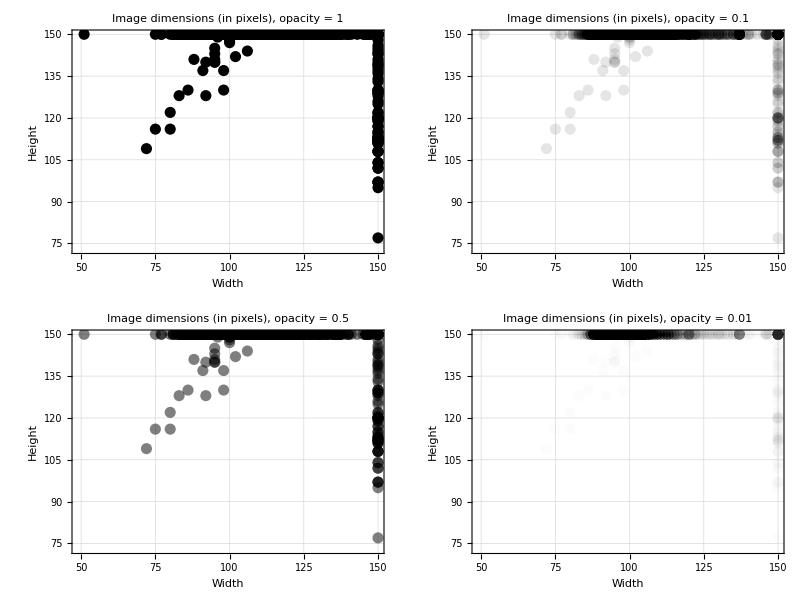
VISUALISATION:
OPACITY -Graphics-

```mathematica
ListPlot[imageDimensions,PlotRange->All,PlotStyle->{Black,Opacity[#],PointSize[.02]},PlotTheme->"Detailed",FrameLabel->{"Width","Height"},PlotLabel->"Image dimensions (in pixels), opacity = "<>ToString[#],ImageSize->400]&/@
{1,0.5,0.1,0.01}//
Multicolumn[#,Spacings->{3,3}]&//
Echo[#,Column[{"VISUALISATION:","OPACITY"}]]&;
```

A better way to visualise this data is to use a 3D histogram or a density histogram. But even with those, we must set our options carefully, or else, we'll fall into the same trap.

```mathematica
Manipulate[
Column[{
Text@Column[{"Distibution of image dimensions (in pixels)",Style[StringJoin["bin = "<>ToString@bins,", height = "<>ToString@height],Orange]},Alignment->Center],
Row[{
Histogram3D[imageDimensions,{bins,height},PlotTheme->"Detailed",PlotLabel->"Histogram3D",ImageSize->400],
DensityHistogram[imageDimensions,{bins,height},PlotTheme->"Detailed",PlotLabel->"DensityHistogram",ImageSize->300]
},Spacer[50]]
},Alignment->Center,Spacings->2],
{{bins,10,"Bin width"},5,50,5},
{{height,10,"Height"},5,50,5}
]//
Echo[#,Column[{"VISUALISATION:","GRANULARITY"}]]&;
```

VISUALISATION:
GRANULARITY

```mathematica
(* these are the books with the tallest and widest covers *)
Show[#,ImageSize->{Automatic,300}]&/@
{
Part[coverImages,Echo[Position[imageDimensions,First@MinimalBy[imageDimensions,First]]⟦1,1⟧,"longest image:"]],
Part[coverImages,Echo[Position[imageDimensions,First@MinimalBy[imageDimensions,Last]]⟦1,1⟧,"widest image"]]
}
```

longest image: 2882

widest image 3463

{-Graphics-,-Graphics-}

Interestingly they were both published a very long time ago! But of course, their publishing date may not have anything to do with the cover dimensions.

From the histogram we can see that the majority of our images have a width of around 90-100 pixels, and a height of around 150 pixels. We can conform all of our images to this dimensions. 
But first let’s see the covers at the extremes.

```mathematica
EntityValue[#,"Dataset"]&/@booksWithCover⟦{2882,3463}⟧
```

{,}

```mathematica
(* random images in their original dimensions *)
randImages=RandomSample[coverImages,5];
Labeled[Show[#,ImageSize->{100,Automatic}],ImageDimensions@#]&/@%
```

{-Graphics-{105,150},-Graphics-{94,150},-Graphics-{100,150},-Graphics-{97,150},-Graphics-{100,150}}

```mathematica
(* images conformed to fit the maximum width in random set *)
conformedImages=Labeled[Show[#,ImageSize->{100,Automatic}],ImageDimensions@#]&/@ConformImages[randImages,Automatic,"Stretch"]
```

{-Graphics-{100,150},-Graphics-{100,150},-Graphics-{100,150},-Graphics-{100,150},-Graphics-{100,150}}

```mathematica
conformedCoverImages=ConformImages[coverImages,{50,50}];
```

Colour profiles and dominant colours

```mathematica
(* get colour profile for a random book cover *)
{Show[#,ImageSize->150],DominantColors[#,4,{"NearestHTMLColor","Coverage","CoverageImage"},"Dataset"],ChromaticityPlot3D[#,"RGB",ImageSize->300]}&@RandomChoice@coverImages
```

{-Graphics-,,-Graphics3D-}

There are patterns everywhere, which do we choose to focus on?

```mathematica
(* we want generality but also accuracy  *)
Block[{img=RandomChoice@coverImages},
Table[
{Show[#,ImageSize->80],DominantColors[#,colourNum,{"NearestHTMLColor","Coverage","CoverageImage"},"Dataset"]}&@img,
{colourNum,{1,3,5}}]//Grid]
```

-Graphics- | 
-Graphics- | 
-Graphics- |

Visualisation is a powerful tool

```mathematica
(* a random sample of 250 images *)
randImages=RandomSample[conformedCoverImages,250];
```

```mathematica
(* feature space plot with greater specificity, less generalization (slower because it's applying the DominantColors func. to each image) *)
FeatureSpacePlot[randImages,FeatureExtractor->(DominantColors[#,1]&),Method->{"TSNE","Perplexity"->20},PlotTheme->"Detailed",ImageSize->600,PlotRange->All,PerformanceGoal->"Speed"]
```

-Graphics-

```mathematica
(* feature space plot with less specificity, greater generalization (faster because pixel values are a lot quicker to extract than dominant colours) *)
FeatureSpacePlot[randImages,FeatureExtractor->{"PixelVector","DimensionReducedVector"},Method->{"TSNE","Perplexity"->20},PlotTheme->"Detailed",ImageSize->600,PlotRange->All,PerformanceGoal->"Speed"]
```

-Graphics-

## 4. Algorithm design

1. Learn the colour features of book covers

```mathematica
(* train a feature extraction function which simply learns dominant colors *)
fe=FeatureExtraction[randImages,(DominantColors[#,1]&),RandomSeeding->1984,PerformanceGoal->"Speed"];
```

2. Apply “learning” to a new bookshelf

```mathematica
newRandImages=RandomSample[conformedCoverImages,250];
```

```mathematica
(* use the FE function on sample set *)
features=fe[newRandImages];
```

```mathematica
(* order sample set based on extracted features *)
ordering=FindShortestTour[features,DistanceFunction->(ColorDistance[#1,#2]&)]⟦2⟧;
```

```mathematica
(* create a collage of book covers ordered by color *)
ImageCollage[newRandImages⟦ordering⟧,ImageSize->500]
```

-Graphics-

There are more sophisticated ways to extract sorting features for a problem such as this.

But we should aim for a good balance between accuracy, and simplicity and speed of the algorithm.

If a more sophisticated algorithm will only marginally improve the results, then it may not be worth it—at least for this particular problem.

## 5. More on the Wolfram Language and real-world data

Book authors and titles

```mathematica
(* book authors *)
bookAuthors=DeleteMissing@EntityValue[allWLBooks,EntityProperty["Book","Author"]];
```

```mathematica
Take[ReverseSortBy[Tally[bookAuthors],Last],20]
```

{{{R. L. Stine},180},{{Carolyn Keene},175},{{Bonnie Bryant},144},{{W. E. Johns},98},{{John Buchan},85},{{Isaac Asimov},73},{{Edgar Rice Burroughs},61},{{Philip K. Dick},60},{{Jack Vance},55},{{L. Sprague de Camp},53},{{Frederik Pohl},53},{{Orson Scott Card},51},{{Jules Verne},50},{{Alan Dean Foster},49},{{Stephen King},47},{{Rex Stout},47},{{Dean Koontz},44},{{Harry Turtledove},43},{{Jude Watson},42},{{Terry Pratchett},41}}

```mathematica
(* book titles *)
bookTitles=DeleteMissing@EntityValue[allWLBooks,EntityProperty["Book","Name"]];
```

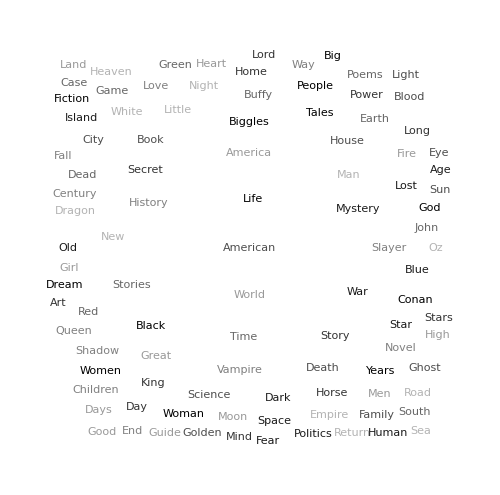
-Graphics- |  -  - Life214
 -  - American178
 -  - World177
 -  - War158
 -  - Time150
 -  - Man134
 -  - Story126
 -  - History119
 -  - Black116
 -  - Book113
 -  - America110
 -  - Mystery109
 -  - Stories108
 -  - New100
 -  - Secret97
 -  - Vampire92
 -  - Biggles89
 -  - House85
 -  - Great80
 -  - Dark78

```mathematica
(* wordcloud plot of publishers *)
Block[{txt=bookTitles,tally},
tally=ReverseSortBy[Tally@DeleteCases[DeleteStopwords@Flatten@TextWords[txt],w_/;(StringLength[w]<2||StringContainsQ[w,DigitCharacter|PunctuationCharacter])],Last];
Grid[{{
WordCloud[tally,IgnoreCase->True,FontWeight->"Light",
WordSpacings->{5,5},ImageSize->500,PlotTheme->"Monochrome"],
Column[Row[#," - "]&/@Take[tally,UpTo@20],Alignment->"-"]
}},Dividers->{Center, False},FrameStyle->Directive[Gray,Dotted],Alignment->Center,Spacings->{3, 0}]
]
```

Languages

```mathematica
(* get book langs *)
booksLangs=DeleteMissing@EntityValue[allWLBooks,EntityProperty["Book","OriginalLanguage"]];
```

```mathematica
ReverseSortBy[Last]@Tally[booksLangs]
```

{{English,9443},{French,129},{Spanish,77},{German,75},{{Ancient Greek},69},{Japanese,55},{Chinese,38},{Latin,35},{Russian,25},{Polish,20},{Italian,19},{Norwegian,17},{{French},13},{Sanskrit,12},{Swedish,11},{Turkish,10},{Greek,8},{Portuguese,5},{Persian,5},{Hebrew,5},{Egyptian,5},{Dutch,5},{{Middle English},4},{Pali,4},{Hindi,4},{Bengali,4},{{Japanese,English},3},{Welsh,3},{Urdu,3},{Danish,3},{Avestan,3},{Arabic,3},{{Portuguese},2},{{Old English},2},{{English},2},{Yiddish,2},{{Latin,Italian,Hebrew},1},{{Hebrew,Ancient Greek,Old Aramaic},1},{{German,Italian,French},1},{{English,Latin},1},{{English,French},1},{{English,Danish},1},{{Coptic,Modern Greek},1},{{Arabic,Persian},1},{{Sanskrit},1},{{Old Japanese},1},{{Irish},1},{{German},1},{{Dari Zoroastrian},1},{Tibetan,1},{Tamil,1},{Sumerian,1},{Serbian,1},{OldAramaic,1},{NahuatlClassical,1},{Hungarian,1},{Finnish,1},{Czech,1},{Belarussian,1}}

Dates

```mathematica
(* get publication dates *)
booksWithCoverPubDates=EntityValue[allWLBooks,EntityProperty["Book","FirstPublished"]];
validDates=Cases[booksWithCoverPubDates,_DateObject];
```

```mathematica
MinMax@validDates
```

{Year: -2250,Day: Wed 16 Oct 2019}

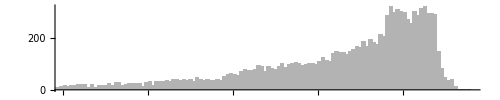

```mathematica
DateHistogram[validDates,"Year",PerformanceGoal->"Speed",AspectRatio->1/5,PlotRange->{{DateObject[{1900,1,1},"Day","Gregorian",1.],Now},All},
PlotTheme->"Monochrome",PlotRangeClipping->True,AspectRatio->1/5,ImageSize->500
]
```

Publishers and companies

```mathematica
(* get publishers *)
booksWithCoverPublishers=EntityValue[allWLBooks,EntityProperty["Book","Publisher"]];
```

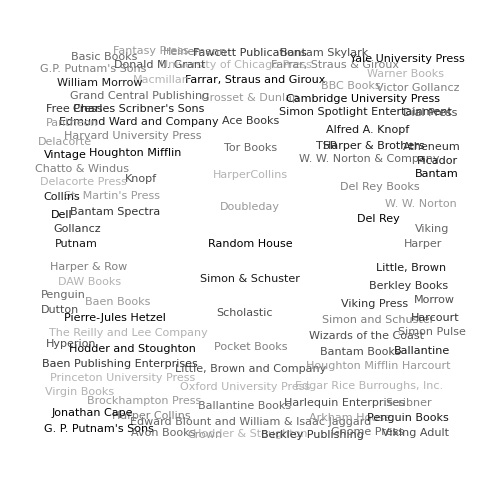
-Graphics- |  -  - Random House375
 -  - Scholastic331
 -  - Doubleday295
 -  - Simon & Schuster286
 -  - Tor Books253
 -  - Ace Books195
 -  - Pocket Books188
 -  - HarperCollins179
 -  - Knopf152
 -  - Del Rey144
 -  - Grosset & Dunlap126
 -  - Alfred A. Knopf109
 -  - Oxford University Press105
 -  - Viking Press101
 -  - Ballantine Books93
 -  - Del Rey Books89
 -  - Baen Books87
 -  - Little, Brown and Company82
 -  - Houghton Mifflin82
 -  - Harper71

```mathematica
(* wordcloud plot of publishers *)
Block[{txt=DeleteMissing@booksWithCoverPublishers,tally},
tally=ReverseSortBy[Tally@txt,Last];
Grid[{{
WordCloud[txt,IgnoreCase->True,FontWeight->"Light",
WordSpacings->{5,5},ImageSize->500,PlotTheme->"Monochrome"],
Column[Row[#," - "]&/@Take[tally,UpTo@20],Alignment->"-"]
}},Dividers->{Center, False},FrameStyle->Directive[Gray,Dotted],Alignment->Center,Spacings->{3, 0}]
]
```

Random House is a part of Penguin Random House (merger between’s Bertelsmann’s Random House and Pearson’s Penguin).

```mathematica
(* Wiki article summary *)
WikipediaData["Random House","SummaryPlaintext"]
```

Random House is an American book publisher and the largest general-interest paperback publisher in the world. It is part of Penguin Random House, which is owned by German media conglomerate Bertelsmann.

```mathematica
(* interpret Penguin as a company *)
Interpreter["Company"|"ComputedCompany"|"Financial"]["Penguin"]
```

Pearson

```mathematica
(* get Company data for Scholastic Corp. it's a lot of data! *)
{#,EntityValue[#,"Dataset"]}&@CompanyData["ScholasticCorporation::4s697"]
```

{Scholastic,}

## The End

## References

[Slide 1]  Elaine Kao, Exploring Computational Thinking
Google AI Blog, Oct. 2010